```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
<<Quaternions`
```

```mathematica
(* Code to generate a group based on its generators and composition rule, this is brute force, can easily blow up if your generators are not closed under multiplication, or are too big *)

GenerateGroupElements[generators_,compose_]:=FixedPoint[Union[#,compose@@@Tuples[#,2]]&,generators];
(* Q8 group = <i,j,k>, composition: quaternion product *)
quaternionGroupElements = GenerateGroupElements[
{Quaternion[0,1,0,0], Quaternion[0,0,1,0], Quaternion[0,0,0,1]}, 
(#1 ** #2)&
];

quaternionGroupPermutations = (el=#;
FindPermutation[quaternionGroupElements,(el ** #)& /@ quaternionGroupElements]
)&  /@ quaternionGroupElements;
QuaternionGroup = PermutationGroup[quaternionGroupPermutations ];

quaternionNames = Association[{
Quaternion[1,0,0,0]->"1", Quaternion[0,1,0,0]->"i", Quaternion[0,0,1,0]->"j",Quaternion[0,0,0,1]->"k",
Quaternion[-1,0,0,0]->"-1", Quaternion[0,-1,0,0]->"-i", Quaternion[0,0,-1,0]->"-j",Quaternion[0,0,0,-1]->"-k"
}];
quaternionPermutationNames = AssociationThread[quaternionGroupPermutations,quaternionNames /@ quaternionGroupElements]

(* Pauli group = <X,Y,Z>, composition: matrix dot product *)
pauliGroupMatrices = GenerateGroupElements[
{PauliMatrix[1], PauliMatrix[2], PauliMatrix[3]},
(#1 . #2)&
];


pauliGroupPermutations = (el=#;
FindPermutation[pauliGroupMatrices,(el . #)& /@ pauliGroupMatrices]
)&  /@ pauliGroupMatrices;
```

<|Cycles[(1 | 8
2 | 7
3 | 6
4 | 5)]→-1,Cycles[(1 | 2 | 8 | 7
3 | 4 | 6 | 5)]→-i,Cycles[(1 | 3 | 8 | 6
2 | 5 | 7 | 4)]→-j,Cycles[(1 | 4 | 8 | 5
2 | 3 | 7 | 6)]→-k,Cycles[(1 | 5 | 8 | 4
2 | 6 | 7 | 3)]→k,Cycles[(1 | 6 | 8 | 3
2 | 4 | 7 | 5)]→j,Cycles[(1 | 7 | 8 | 2
3 | 5 | 6 | 4)]→i,Cycles[{}]→1|>

```mathematica
PauliGroup = PermutationGroup[pauliGroupPermutations];
```

```mathematica
ScalarMultiple[m1_,m2_]:=(
{r1,c1}=Position[m1,x_/;x!=0][[1]];
{r2,c2}=Position[m2,x_/;x!=0][[1]];
If[r1==r2 && c1==c2 && m1[[r1,c1]]/m2[[r2,c2]]*m2==m1, m1[[r1,c1]]/m2[[r2,c2]], "no"]
)
```

```mathematica
ScalarMultiple[X,Y]
```

no

```mathematica
pauliMatrixNames= Association[{0->"I", 1->"X", 2->"Y",3->"Z"}];
```

```mathematica
PauliGroupElementName[m_]:=(
basePauli = Select[ Range[0,3], ScalarMultiple[m, PauliMatrix[#]]!="no"&][[1]];
sm= ScalarMultiple[m, PauliMatrix[basePauli]];
baseName = pauliMatrixNames[basePauli];
If[sm == 1, baseName, StringReplace[ToString[sm],{"I"->"i","1"->""}]<> baseName]
)
```

```mathematica
pauliGroupElementMatrixNames = PauliGroupElementName /@ pauliGroupMatrices
```

{-I,-Z,-X,-iY,-iX,Y,-Y,iX,iY,X,-iI,-iZ,iZ,iI,Z,I}

```mathematica
pauliGroupPermutationNames = AssociationThread[pauliGroupPermutations,pauliGroupElementMatrixNames];
```

```mathematica
a
```

a

```mathematica
Association[]
```

<||>

```mathematica
CommutationProbability[group_]:=Count[Tuples[GroupElements[group], 2],x_/;PermutationProduct[x[[1]], x[[2]]] == PermutationProduct[x[[2]],x[[1]]]]/GroupOrder[group]^2
```

```mathematica
CommutationProbability[PauliGroup]
```

5/8

```mathematica
N[%]*100
```

62.5

```mathematica
Matrix
```

Matrix

```mathematica
Count[Tuples[GroupElements[DihedralGroup[4]],2],x_/;x[[1]]==Cycles[{{}}]]
```

8

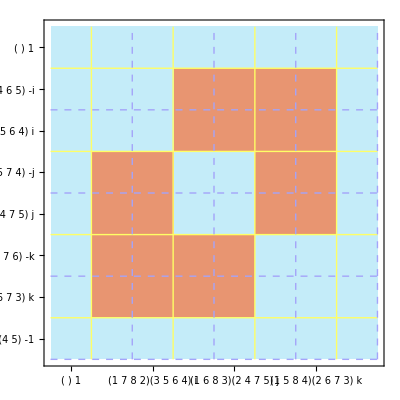

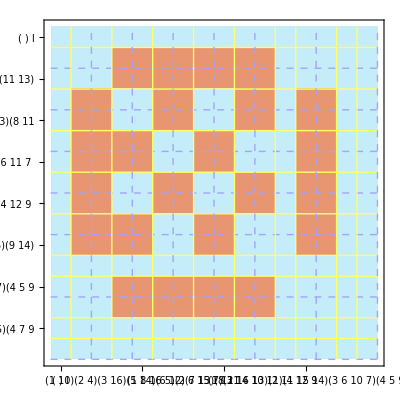

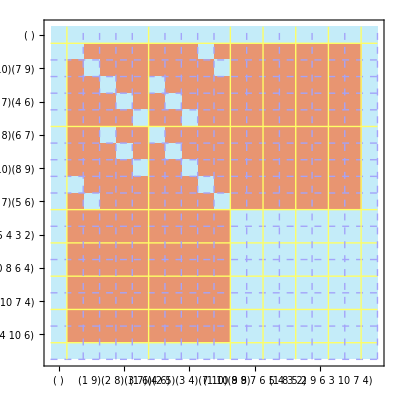

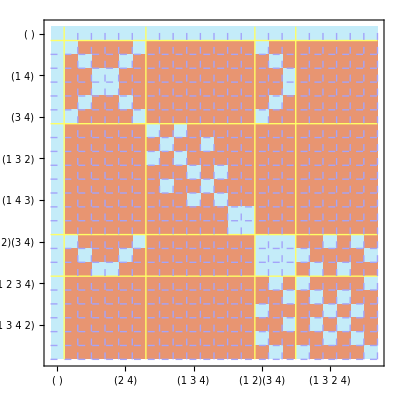

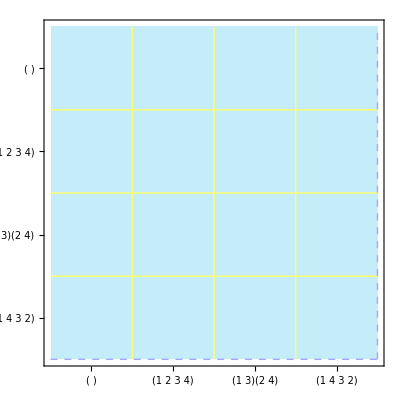

```mathematica
Options[CommutatorPlot]={"Ticks"->True, "PermutationNames"-><||>};
CommutatorPlot[group_, OptionsPattern[]]:=Module[{els, n, CycleLengths, ConjClasses, conjClasses, ConjClass, ConjClassId, colorList, conjugacyClassColor, regularGridColor, notCommutingColor, commutingColor, indexed, ConjClassSeparator,tickers, markers,mx},

els=GroupElements[group];
n=Length[els];

(* Initial sorting of elements provides a good approximation for sorting by conjugacy class, 
	and provides a sorting for the conjugacy classes themselves *)

CycleLengths[c_]:=Sort[Length /@ c[[1]]];
els=SortBy[GroupElements[group], Function[g,{CycleLengths[g],g}]];

(* Calculating and sorting by conjugacy classes *)
ConjClass[g_,el_]:=GroupOrbits[g, {el}];
ConjClasses[g_]:=DeleteDuplicates[
Table[
{ConjClass[g,GroupElements[g][[i]]]}, 
{i, 1, GroupOrder[g]}
]
];
conjClasses=ConjClasses[group];
ConjClassId[el_]:=Position[conjClasses, {ConjClass[group, el]}][[1]][[1]];
els=SortBy[GroupElements[group], Function[g,{ConjClassId[g],g}]];

(************** Formattings ****************)

colorList = ColorData[45,"ColorList"];
conjugacyClassColor=colorList[[5]];
regularGridColor=colorList[[10]];

commutingColor=colorList[[3]];
notCommutingColor=colorList[[7]];


indexed=Thread[{Range[n], els}];

(* Red grid lines for conjugacy classes *)
ConjClassSeparator[p_]:=Not[
p[[1]]+1>Length[indexed]||
p[[1]]+1<=Length[indexed]&& ConjClassId[indexed[[p[[1]]]][[2]]]==ConjClassId[indexed[[p[[1]]+1]][[2]]]];
ticks = If[OptionValue["Ticks"], True, False];
permutationNames=OptionValue["PermutationNames"];
tickers=If[ticks,
Function[p, If[ConjClassSeparator[p],{p[[1]],conjugacyClassColor},{p[[1]],{regularGridColor, Dashed}}]] /@ indexed,
Function[p,{p[[1]],conjugacyClassColor}] /@ Select[indexed,ConjClassSeparator]
];

(* Setting up markers with nice formatting of the permutations *)
markers =  If[ticks,
FormatCycle[c_]:=If[c==Cycles[{{}}],"( )",StringReplace[StringJoin[ToString  /@ c[[1]]], {"{"->"(", "}"->")", ","->""}]];
If[Length[permutationNames]>0, 
Function[x,{x[[1]],FormatCycle[x[[2]]] <> "   "<> permutationNames[x[[2]]] } ] /@ indexed,
Function[x,{x[[1]],FormatCycle[x[[2]]]} ] /@ indexed
],
Automatic
];(* Function[x, If[OddQ[First[x]], x, {x[[1]],""} ]] /@ indexed;*)

mx=ArrayReshape[Map[Function[ab,
PermutationProduct[ab[[1]], ab[[2]]] == PermutationProduct[ab[[2]],ab[[1]]]],Tuples[els, 2]],{n,n}];
Return[MatrixPlot[mx, Mesh->{tickers, tickers}, ColorRules->{True->commutingColor, False->notCommutingColor}, FrameTicks->{markers,Map[Function[v, {v[[1]], Rotate[v[[2]], 90 Degree]}],markers]}]]
](* end module*)
CommutatorPlot[QuaternionGroup, {"PermutationNames"->quaternionPermutationNames}]
CommutatorPlot[PauliGroup, {"PermutationNames"->pauliGroupPermutationNames}]
CommutatorPlot[DihedralGroup[10]]
CommutatorPlot[SymmetricGroup[4]]
CommutatorPlot[CyclicGroup[4]]
```

```mathematica
Show[%342,ImageSize->Large]
```

Show::gtype: Out is not a type of graphics.

Show[%342,ImageSize→Large]

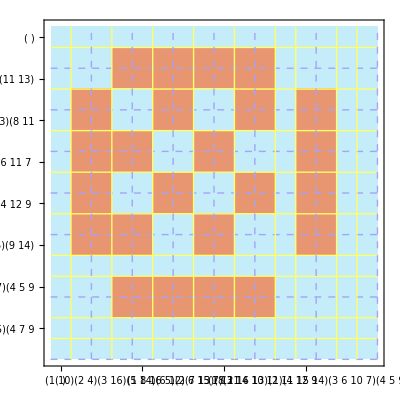

```mathematica
CommutatorPlot[PauliGroup]
```

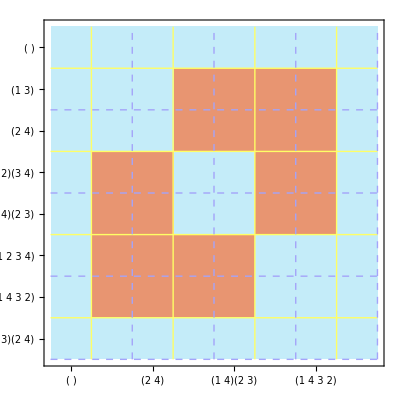

```mathematica
CommutatorPlot[DihedralGroup[4]]
```

```mathematica
CommutatorPlot[DihedralGroup[10]]
```

-Graphics-